## Tupik_D_L

## Lab_work_7: Статический анализ

## Элементарная описательная статистика

```mathematica
data=RandomReal[{1,100},9]
```

{48.788,34.4159,33.3842,49.1463,71.8922,68.9701,53.9519,44.5591,77.3902}

```mathematica
Mean[data]
```

53.6109

```mathematica
Sort[data]
```

{33.3842,34.4159,44.5591,48.788,49.1463,53.9519,68.9701,71.8922,77.3902}

```mathematica
Median[data]
```

49.1463

```mathematica
Max[data]
```

77.3902

```mathematica
Min[data]
```

33.3842

```mathematica
Variance[data]
```

254.797

```mathematica
StandardDeviation[data]
```

15.9624

```mathematica
Quantile[data,1/2]
```

49.1463

```mathematica
Quartiles[data]
```

{42.0233,49.1463,69.7007}

## Работа со статистическими распределениями

```mathematica
PDF[NormalDistribution[μ,σ],x] (*дает функцию плотности вероятности для распределения, оцененного в точке x.*)
PDF[NormalDistribution[1,3],3]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 ⅇ^(2/9) √(2 π))

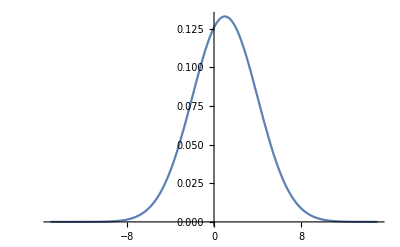

```mathematica
Plot[PDF[NormalDistribution[1,3],x],{x,-15,15}]
```

```mathematica
Mean[BinomialDistribution[1000,.1]]
```

100.

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] (*дает характеристическую функцию для распределения в зависимости от переменной t.*)
CharacteristicFunction[CauchyDistribution[μ,σ],t]  (*распределени коши*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

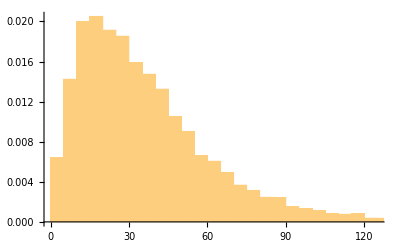

```mathematica
data=RandomVariate[GammaDistribution[2,18],10000];hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

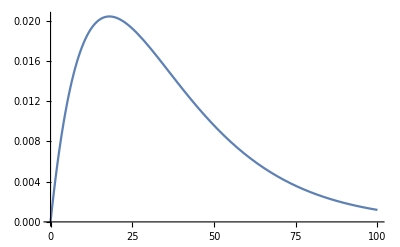

```mathematica
pl=Plot[PDF[GammaDistribution[2,18],x],{x,0,100}]
```

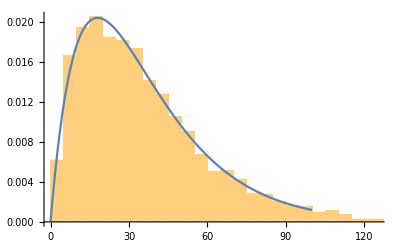

```mathematica
Show[hist,pl]
```

## Город Брест и Минск (сравнение по температуре)

```mathematica
brest = DateListPlot[WeatherData["Brest","Temperature",{{2022,6,1},{2022,6, 30},"Day"}],Joined->True];
```

```mathematica
minsk = DateListPlot[WeatherData["Minsk","Temperature",{{2022,6,1},{2022,6,30},"Day"}],Joined->True, PlotStyle->Red];
```

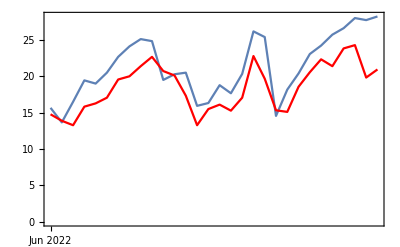

```mathematica
Show[brest, minsk]
```

```mathematica
CityData["Brest", "Population"]
```

318000 people

```mathematica
Sunset[LinguisticAssistant]
```

Minute: Sun 18 Dec 2022 17:14GMT+3

## Моделирование методом Монте-Карло. Успеть на учёбу

```mathematica
bus=RandomReal[{10,30},1000];
legs = RandomReal[{5,15},1000];
```

```mathematica
k = 0;
```

```mathematica
For[i=1,i<1001,i++,If[bus[[i]] + legs[[i]] > 40, k = k + 1]];
```

```mathematica
(1000-k)/1000.
```

0.933